```mathematica
(*Початоква купа формул*)
ClearAll[x,t,L,Gtailor,G,y,u,uI,t1,t2,x1,x2,T,TI,X,XI,Gx]
L=(D[#,t]-D[#,{x,2}])&
G=(t/Sqrt[4Pi*t]*Exp[-x^2/(4t)])(*/.{t->(t-tI),x->(x-xI)}*)
Gtailor=Simplify[Normal[Series[G,{x,1,2},{t,1,2}]]]/.{t->(t-tI),x->(x-xI)}
G=G/.{t->(t-tI),x->(x-xI)}
y:=Sin[x]*Sin[t]
u := L[y]
uI:=u/.{x->xI,t->tI}
(*Просторово-часова область*)
t1:=1
t2:=50
x1:=1
x2:=50
T:={t,t1,t2}
TI:=T/.{t->tI}
X:={x,x1,x2}
XI:=X/.{x->xI}
```

∂_t #1-∂_{x,2} #1&

(ⅇ^(-x^2/(4 t)) √t)/(2 √π)

(203+(t-tI) (162+244 (x-xI)-102 (x-xI)^2)+(t-tI)^2 (-13-82 (x-xI)+39 (x-xI)^2)-226 (x-xI)+31 (x-xI)^2)/(512 ⅇ^(1/4) √π)

(ⅇ^(-(x-xI)^2/(4 (t-tI))) √(t-tI))/(2 √π)

(352-64 x-32 x^2)/(512 ⅇ^(1/4) √π)

-(ⅇ^(-1.5976 x-0.07056 x^3) (-1.5976-0.21168 x^2))/((1+ⅇ^(-1.5976 x-0.07056 x^3))^2)

(ⅇ^(-x^2/4))/(2 √π)

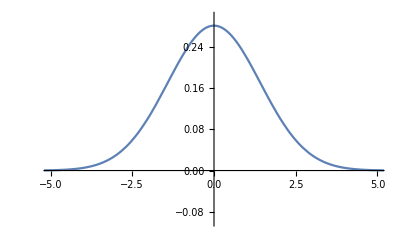

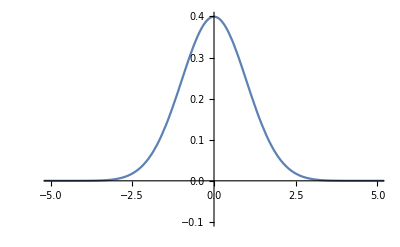

```mathematica
Gtailorx=Gtailor/.{t->1,tI->0,xI->0}
Gtailorx=D[1/(1+Exp[-0.07056 x^3-1.5976 x]),x]
Gx=G/.{t->1,tI->0,xI->0}
Plot[Gx, {x,-10,20},PlotRange->{{-5,5},{-0.1,0.3}}]
Plot[Gtailorx, {x,-10,20},PlotRange->{{-5,5},{-0.1,0.4}}]
```

(8+304 t-56 t^2)/(512 ⅇ^(1/4) √π)

(ⅇ^(-1/4/t) √t)/(2 √π)

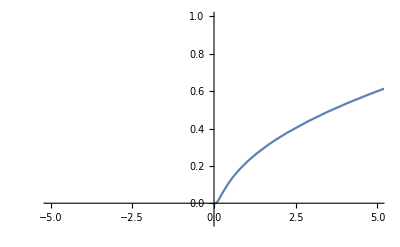

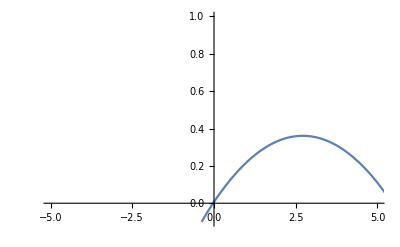

```mathematica
Gtailort=Gtailor/.{x->1,tI->0,xI->0}
Gt=G/.{x->1,tI->0,xI->0}
Plot[Gt, {t,-10,20},PlotRange->{{-5,5},{-0.1,1}}]
Plot[Gtailort, {t,-10,20},PlotRange->{{-5,5},{-0.1,1}}]
```

```mathematica
G*uI
```

(ⅇ^(-(x-xI)^2/(4 (t-tI))) √(t-tI) (Cos[tI] Sin[xI]+Sin[tI] Sin[xI]))/(2 √π)

```mathematica
(*Перший у*)
yInf=Simplify[Integrate[G,Evaluate[XI],Evaluate[TI]]]
```

1/(48 √π)(16 ⅇ^(-((-51+2 t) (-50+x)^2)/(4 (-50+t) (-1+t))) (ⅇ^((-50+x)^2/(4 (-1+t))) (-50+t)^(3/2)-ⅇ^((-50+x)^2/(4 (-50+t))) (-1+t)^(3/2)) (-50+x)-16 ⅇ^(-((-51+2 t) (-1+x)^2)/(4 (-50+t) (-1+t))) (ⅇ^((-1+x)^2/(4 (-1+t))) (-50+t)^(3/2)-ⅇ^((-1+x)^2/(4 (-50+t))) (-1+t)^(3/2)) (-1+x)-2 ⅇ^(-(-50+x)^2/(4 (-50+t))) √(-50+t) (-50+x) (2200+6 t-100 x+x^2)+2 ⅇ^(-(-50+x)^2/(4 (-1+t))) √(-1+t) (-50+x) (2494+6 t-100 x+x^2)+2 ⅇ^(-(-1+x)^2/(4 (-50+t))) √(-50+t) (-1+x) (-299+6 t-2 x+x^2)-2 ⅇ^(-(-1+x)^2/(4 (-1+t))) √(-1+t) (-1+x) (-5+6 t-2 x+x^2)-600 √π (-50+t) Erf[(-50+x)/(2 √(-50+t))]+12 √π (-50+t) t Erf[(-50+x)/(2 √(-50+t))]-√π (-50+x)^4 Erf[(-50+x)/(2 √(-50+t))]+12 √π (-1+t) Erf[(-50+x)/(2 √(-1+t))]-12 √π (-1+t) t Erf[(-50+x)/(2 √(-1+t))]+√π (-50+x)^4 Erf[(-50+x)/(2 √(-1+t))]+600 √π (-50+t) Erf[(-1+x)/(2 √(-50+t))]-12 √π (-50+t) t Erf[(-1+x)/(2 √(-50+t))]+√π (-1+x)^4 Erf[(-1+x)/(2 √(-50+t))]-12 √π (-1+t) Erf[(-1+x)/(2 √(-1+t))]+12 √π (-1+t) t Erf[(-1+x)/(2 √(-1+t))]-√π (-1+x)^4 Erf[(-1+x)/(2 √(-1+t))])

```mathematica
(*Точки для подбудови вектори U*)
(*m0:={{xI->1,tI->-10},{xI->2,tI->-20},{xI->3,tI->-30},{xI->4,tI->-1},{xI->5,tI->-2}}
mE:={{xI->100,tI->1},{xI->200,tI->30},{xI->55,tI->10},{xI->65,tI->20},{xI->75,tI->30}}*)
m0:={{xI->1,tI->-10},{xI->2,tI->-20}}
size0:=Length[m0]
mE:={{xI->100,tI->1},{xI->200,tI->30}}
sizeE:=Length[mE]

(* Області (початкова і гранична) *)
region0:=Boole[t==0&&x≠x2&&x≠x1]
regionE:=Boole[t!=0&&x==x2&&x==x1]
```

```mathematica
Gm0:=G/.m0
GmE:=G/.mE
```

```mathematica
(*Вектор В*)
B11:=Gm0*region0
B12:=GmE*region0
B21:=Gm0*regionE
B22:=GmE*regionE
B:={Join[B11,B12],Join[B21,B22]}
B//MatrixForm
Transpose[B]//MatrixForm
```

((ⅇ^(-(-1+x)^2/(4 (10+t))) √(10+t) Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-(-2+x)^2/(4 (20+t))) √(20+t) Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-(-100+x)^2/(4 (-1+t))) √(-1+t) Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-(-200+x)^2/(4 (-30+t))) √(-30+t) Boole[t==0&&x≠50&&x≠1])/(2 √π)
(ⅇ^(-(-1+x)^2/(4 (10+t))) √(10+t) Boole[t≠0&&x==50&&x==1])/(2 √π) | (ⅇ^(-(-2+x)^2/(4 (20+t))) √(20+t) Boole[t≠0&&x==50&&x==1])/(2 √π) | (ⅇ^(-(-100+x)^2/(4 (-1+t))) √(-1+t) Boole[t≠0&&x==50&&x==1])/(2 √π) | (ⅇ^(-(-200+x)^2/(4 (-30+t))) √(-30+t) Boole[t≠0&&x==50&&x==1])/(2 √π))

((ⅇ^(-(-1+x)^2/(4 (10+t))) √(10+t) Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-(-1+x)^2/(4 (10+t))) √(10+t) Boole[t≠0&&x==50&&x==1])/(2 √π)
(ⅇ^(-(-2+x)^2/(4 (20+t))) √(20+t) Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-(-2+x)^2/(4 (20+t))) √(20+t) Boole[t≠0&&x==50&&x==1])/(2 √π)
(ⅇ^(-(-100+x)^2/(4 (-1+t))) √(-1+t) Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-(-100+x)^2/(4 (-1+t))) √(-1+t) Boole[t≠0&&x==50&&x==1])/(2 √π)
(ⅇ^(-(-200+x)^2/(4 (-30+t))) √(-30+t) Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-(-200+x)^2/(4 (-30+t))) √(-30+t) Boole[t≠0&&x==50&&x==1])/(2 √π))

```mathematica
(*Вектор У з областями*)
Y:={y*region0,y*regionE}
```

```mathematica
By=Integrate[(Transpose[B].Y)/.{t->0},Evaluate[X]]+Integrate[(Transpose[B].Y)/.{x->x1},Evaluate[T]]+Integrate[(Transpose[B].Y)/.{x->x2},Evaluate[T]]
```

{0,0,0,0}

```mathematica
P=PseudoInverse[Integrate[(Transpose[B].B)/.{t->0},Evaluate[X]]+Integrate[(Transpose[B].B)/.{x->x1},Evaluate[T]]+Integrate[(Transpose[B].B)/.{x->x2},Evaluate[T]]]
```

General::ovfl: Overflow occurred in computation.

```mathematica
u0=P[[1;;size0]].By
```

```mathematica
uE=P[[size0+1;;]].By
```

```mathematica
yFull=yInf+Gm0.u0+GmE.uE
yFull
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Indeterminate